```mathematica
LS=2;
mD[p_]:=4 Sin[1/2(2π p)/LS]^2;
MeanLink[λ_]:=If[λ<4,1-λ/8,2/λ];
m2[λ_]:=λ -2 (1-MeanLink[λ]);
G[λ_,p_]:=1/(m2[λ]+mD[p]);
I0[λ_]:=1/LS Sum[mD[p] G[λ,p],{p,0,LS-1}];
I1[λ_]:=1/LS Sum[mD[p] G[λ,p]^2,{p,0,LS-1}];
S0[λ_]:=1/LS Sum[ G[λ,p],{p,0,LS-1}];
Sunset[λ_,p_]:=1/LS^2 Sum[ G[λ,l1] G[λ,l2] G[λ,p-l1-l2],{l1,0,LS-1},{l2,0,LS-1}];
G0[λ_,p_]:=1/LS G[λ,p];
G1[λ_,p_]:=λ 1/LS G[λ,p]^2 I0[λ];
G2[λ_,p_]:=λ^2(1/LS I0[λ]^2 G[λ,p]^3+1/LS G[λ,p]^2(I0[λ] I1[λ] - m2[λ] S0[λ]^2) +1/LS m2[λ]^2 G[λ,p]^2 Sunset[λ,p]);
GExact[λ_,p_]:=If[λ<4,Which[p==0,1/λ-1/16,p==1,1/16,True,0],Which[p==0,1/(2λ)+1/λ^2,p==1,1/(2λ)-1/λ^2]];
SG[λ_,p_,m_]:=Which[m==0,G0[λ,p],m==1,G0[λ,p]+ G1[λ,p],m==2,G0[λ,p]+ G1[λ,p]+G2[λ,p],True,0];
(*For[p0=0,p0≤1,p0++,
Print[Plot[{GExact[λ,p0],SG[λ,p0,0],SG[λ,p0,1],SG[λ,p0,2]},{λ,0.5,8},PlotStyle->{Black,Blue,Green,Red}]];
];*)
λ0=2.3; 
Print["p = 0: ",N[{G0[λ0,0],G1[λ0,0],G2[λ0,0]}]];
Print["p = 1: ",N[{G0[λ0,1],G1[λ0,1],G2[λ0,1]}]];
```

p = 0: {0.289855,0.135013,0.0275959}

p = 1: {0.0873362,0.0122575,-0.00547291}

```mathematica
Expand[FullSimplify[λ (G0[λ,0] + G0[λ,1]),{λ<4}]/.{λ->0}]
Expand[FullSimplify[λ (G1[λ,0] + G1[λ,1]),{λ<4}]/.{λ->0}]
Expand[FullSimplify[λ (G2[λ,0] + G2[λ,1]),{λ<4}]/.{λ->0}]
```

2/3

4/9

8/27

```mathematica
N[2/3+4/9+8/27+16/81]
```

1.60494

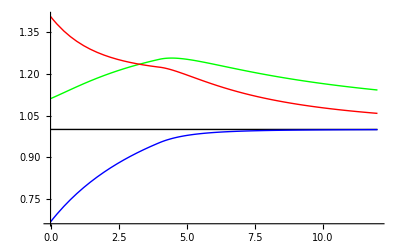

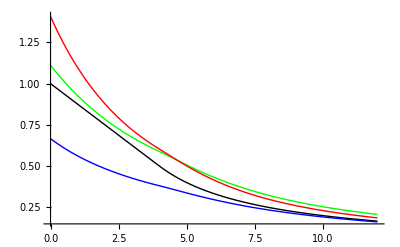

```mathematica
g0g0[λ_,m_]:=λ (SG[λ,0,m]+SG[λ,1,m]);
g0g1[λ_,m_]:=λ (SG[λ,0,m]-SG[λ,1,m]);
g0g1e[λ_]:=If[λ<4,1-λ/8,2/λ];
Plot[{1,g0g0[λ,0],g0g0[λ,1],g0g0[λ,2]},{λ,0,12},PlotStyle->{Black,Blue,Green,Red}]
Plot[{g0g1e[λ],g0g1[λ,0],g0g1[λ,1],g0g1[λ,2]},{λ,0,12},PlotStyle->{Black,Blue,Green,Red}]
```

```mathematica
N[4 π^3]
```

124.025

```mathematica
F[χ0_,χ1_,λ_]:= χ0/2(λ(1+χ0^2)(1+χ1^2)+2(1-χ1^2)+4χ0 χ1)/(1 + χ0^2);
NSolve[{χ1==F[χ0,χ1,0],χ0==F[χ1,χ0,0]},{χ0,χ1}]
```

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$Aborted

```mathematica
Clear[χ0,χ1];
λ0=0.7;
S[χ0_,χ1_,λ_]:=λ Log[1+χ0^2]+λ Log[1+χ1^2]-((1-χ0^2)(1-χ1^2)+4χ0 χ1)/((1+χ0^2)(1+χ1^2));
GrP={};
For[itrial=1,itrial≤1000,itrial++,
χ0i=RandomReal[{-10.0,10.0}];χ1i=RandomReal[{-10.0,10.0}];
Res1=FindRoot[{-4 χ1+2 χ0 (2+2 (χ0-χ1) χ1+λ0 (1+χ0^2) (1+χ1^2))==0,2 (2 χ0 (-1+χ1^2)+χ0^2 χ1 (-2+λ0+λ0 χ1^2)+χ1 (2+λ0+λ0 χ1^2))==0},{{χ0,χ0i},{χ1,χ1i}}];
Pt1={χ0,χ1,S[χ0,χ1,λ0]}/.Res1;
GrP=Join[GrP,{Blue,PointSize[0.05],Point[Pt1]}];
];
Gr1=Plot3D[S[χ0,χ1,λ0],{χ0,-5,5},{χ1,-5,5}];
Show[Gr1,Graphics3D[GrP]]
```

-Graphics3D-

```mathematica
FullSimplify[D[λ Log[1+χ0^2]+λ Log[1+χ1^2]-((1-χ0^2)(1-χ1^2)+4χ0 χ1)/((1+χ0^2)(1+χ1^2)),χ0]]
```

(-4 χ1+2 χ0 (2+2 (χ0-χ1) χ1+λ (1+χ0^2) (1+χ1^2)))/((1+χ0^2)^2 (1+χ1^2))

```mathematica
Clear[λ];
FullSimplify[2 (2 χ0 (-1+χ1^2)+χ0^2 χ1 (-2+λ+λ χ1^2)+χ1 (2+λ+λ χ1^2))]
```

2 (2 χ0 (-1+χ1^2)+χ0^2 χ1 (-2+λ+λ χ1^2)+χ1 (2+λ+λ χ1^2))

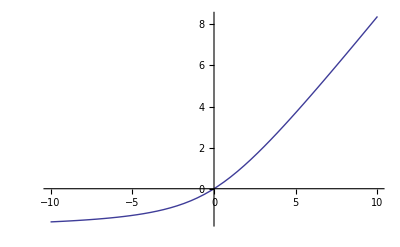

```mathematica
Plot[λ/2-2+√(4+λ^2/4),{λ,-10,10}]
```